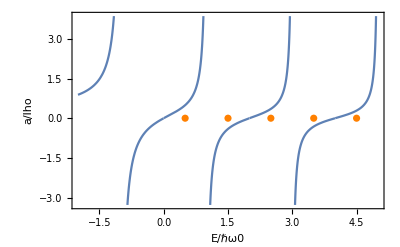

```mathematica
Clear["Global`*"];
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
um=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;mNa = 23amu;
a0= 5.2917721067 10^-11;
ϵ0=8.854187817 10^-12;
c=299792458;
cm=10^-2;
ms=10^-3;
ωrCs=2π 150kHz;
ωaCs=2π 25kHz;
ωrNa=2π 150kHz;
ωaNa=2π 25kHz;
μ=(mNa mCs)/(mCs+mNa);
ωz=1. (ωrCs^2 ωaCs)^(1/3);ωaCs;
lho=√(ℏ/(μ ωz));
Clear[aRed,aS]
aS[e_]:=aS[e]=(1/2)(Gamma[1/4-e/2-3/4]/Gamma[3/4-e/2-3/4]);
Show[{
Plot[aS[e],{e,-2,5},Axes->False,Frame->True,FrameLabel->{"E/ℏω0","a/lho"},GridLines->{{#,Dashed}&/@Range[1/2,10,2],{0}}],
ListPlot[{1/2+#,0}&/@Range[0,10],PlotStyle->Orange]
}]
```

```mathematica
as=513a0;219.607 a0;
at=33a0;247.462 a0;
aUp=at;
aDown=0.4375as+0.5625at; (*flip Cs*)

eUp=e/.Solve[aS[e]==aUp/lho&&e>0&&e<5/2,e][[1]]
eDown=e/.Solve[aS[e]==aDown/lho&&e>0&&e<5/2,e][[1]]
(eUp) ωz /2/π
(eDown) ωz/2/π
(eUp ωz -eDown ωz)/2/π
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.0251132

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.188271

2073.05

15541.4

-13468.4